```mathematica
(*Solving for the closed and open Kitaev chains, plotting energies and checking the zero-energy modes against the topological invariant.*)
Clear["Global`*"]
SetDirectory["D:\\compphys\\majorana1"];
$PrePrint=#/.out_->TraditionalForm[out]&;
Dagger[m_]:=ConjugateTranspose[m]
MakeReal[xvar_]:={Im[xvar]^=0;Re[xvar]^=xvar;xvar*^=xvar;}
(*Pfaffian of a matrix. See https://en.wikipedia.org/wiki/Talk%3APfaffian#Mathematica_code.*)
Pf[A_]:=If[Length[A]==0,1,Module[{L,A1,MatrixDelete},MatrixDelete[M_,i_]:=Delete[#,i]&/@Delete[M,i];
L=Length[A];A1=MatrixDelete[A,1];
Sum[(-1)^i (A[[1]][[i]] Pf[MatrixDelete[A1,i-1]]),{i,2,L}]]]
σ[i_]:=PauliMatrix[i];
ZeroMat[n_]:=ConstantArray[0,{n,n}];
Id[n_]:=IdentityMatrix[n];
```

```mathematica
MakeReal[t];MakeReal[k];MakeReal[μ];MakeReal[Δ];
(*Bulk energies.*)
ϵ=Sqrt[(2t*Cos[k]+μ)^2+4Δ^2*Sin[k]^2]
(*Hamiltonian.*)
H1=(-2t*Cos[k]-μ)*PauliMatrix[3]-2*Δ*Sin[k]*PauliMatrix[2]
U={{1,1},{ⅈ,-ⅈ}};
(*Antidiagonal Hamiltonian.*)
H1anti=FullSimplify[(ⅈ/2)U.H1.Dagger[U]]
(*k=0 the Hamiltonian is real antisymmetric.*)
zero=H1anti/.k->0
(*k=π the Hamiltonian is real antisymmetric.*)
pi=H1anti/.k->π
(*Calculate topological invariant.*)
TopInv=Sign[Pf[zero]*Pf[pi]]
```

√(4 Δ^2 sin^2(k)+(2 t cos(k)+μ)^2)

(-μ-2 t cos(k) | 2 ⅈ Δ sin(k)
-2 ⅈ Δ sin(k) | μ+2 t cos(k))

(0 | -μ-2 t cos(k)-2 ⅈ Δ sin(k)
μ+2 t cos(k)-2 ⅈ Δ sin(k) | 0)

(0 | -2 t-μ
2 t+μ | 0)

(0 | 2 t-μ
μ-2 t | 0)

sgn((-μ-2 t) (2 t-μ))

```mathematica
(*Plot bulk energies + topological invariant with variable μ, t, and Δ.*)
(*The blue/yellow lines are energies, green line is topological invariant.*)
Manipulate[Plot[Evaluate[{ϵ,-ϵ,TopInv}/.{μ->μVal,t->tVal,Δ->ΔVal}],{k,-π,π}, AxesLabel->{"k","E"}],{μVal,-3,3},{tVal,-3,3},{ΔVal,-5,5}]
```

```mathematica
(*Finite Kitaev ring energy as a function of λ which controls whether its antiperiodic, open, or periodic.*)
FermionSites=200;
DiagMat=DiagonalMatrix[Table[μ,{n,1,FermionSites}]]+DiagonalMatrix[Table[t,{n,1,FermionSites-1}],1]+DiagonalMatrix[Table[t,{n,1,FermionSites-1}],-1]+Normal@SparseArray[{{1,FermionSites}->λ*t,{FermionSites,1}->λ*t}];
OffDiagMat=DiagonalMatrix[Table[-Δ,{n,1,FermionSites-1}],1]+DiagonalMatrix[Table[Δ,{n,1,FermionSites-1}],-1];

HMat=ArrayFlatten[{{DiagMat,OffDiagMat},{OffDiagMat†,-DiagMat}}];

MinVal=1;MaxVal=3;Incr=0.05;
λMin=-1;λMax=1;
Do[RingEList[μ]={};,{μ,MinVal,MaxVal,Incr}]

Do[AppendTo[RingEList[μ],Sort[Eigenvalues[HMat/.{Δ->1,t->1,λ->n}]]],{n,λMin,λMax,Incr},{μ,MinVal,MaxVal,Incr}];//AbsoluteTiming
Manipulate[ListLinePlot[RingEList[μ]ᵀ,DataRange->{λMin,λMax},PlotRange->{Automatic,{-1,1}},PlotStyle->Black,ImageSize->1400,TicksStyle->20,AxesLabel->{"λ","E/t"},AxesStyle->30,PlotLabel->Style[StringForm["N = `` and μ/t = ``.",FermionSites,μ],FontSize->40]],{μ,MinVal,MaxVal,Incr}]
```

{79.55016,Null}

{2.51395,Null}

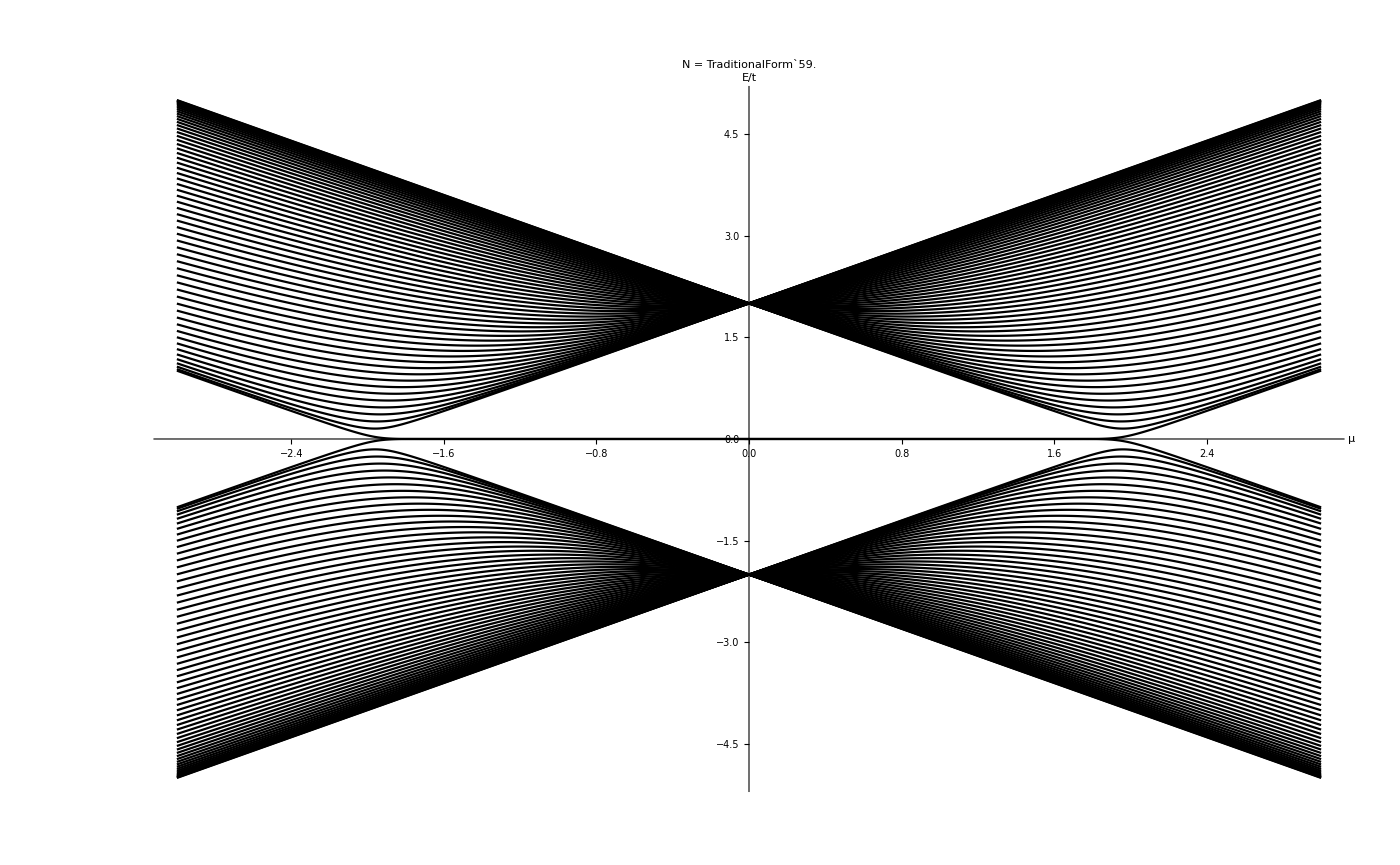

```mathematica
(*Plotting energies of open Kitaev chain.*)
FermionSites=59;
DiagMat=DiagonalMatrix[Table[μ,{n,1,FermionSites}]]+DiagonalMatrix[Table[t,{n,1,FermionSites-1}],1]+DiagonalMatrix[Table[t,{n,1,FermionSites-1}],-1];
OffDiagMat=DiagonalMatrix[Table[-Δ,{n,1,FermionSites-1}],1]+DiagonalMatrix[Table[Δ,{n,1,FermionSites-1}],-1];

HMat=ArrayFlatten[{{DiagMat,OffDiagMat},{OffDiagMat†,-DiagMat}}];

OpenEList={};MinVal=-3;MaxVal=3;Incr=0.01;
Do[AppendTo[OpenEList,Sort[Eigenvalues[HMat/.{μ->n,Δ->1,t->1}]]],{n,MinVal,MaxVal,Incr}]//AbsoluteTiming

ListLinePlot[OpenEListᵀ,DataRange->{MinVal,MaxVal},PlotStyle->Black,ImageSize->1400,TicksStyle->20,AxesLabel->{"μ","E/t"},AxesStyle->30,PlotLabel->Style[StringForm["N = ``.",FermionSites],FontSize->40]]
```